### More accurate entropy values

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, 3], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
ListStepPlot[Callout[#1, #2, Above,LabelVisibility->All]&@@@SortBy[entaps, First], LabelingSize->Large]]
```

-Graphics-

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, 4], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
ListStepPlot[Callout[#1, #2, Above,LabelVisibility->All]&@@@SortBy[entaps, First], LabelingSize->Large]]
```

Without canonicalization

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, 4], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
ListStepPlot[Callout[#1, #2, Above,LabelVisibility->All]&@@@SortBy[entaps, First], LabelingSize->Large]]
```

-Graphics-

```mathematica
Labeled[]
```

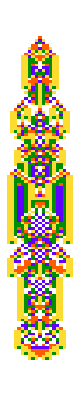
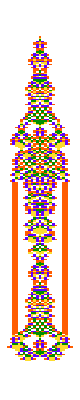
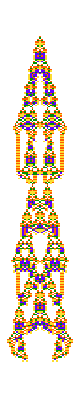
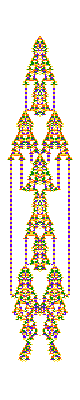
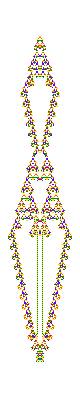
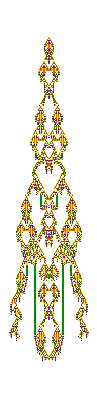
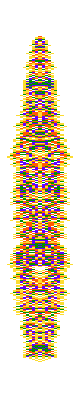
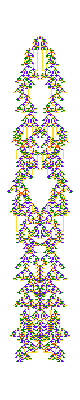
{-Graphics-7.31655,-Graphics-7.57712,-Graphics-7.81197,-Graphics-8.07962,-Graphics-8.12681,-Graphics-8.35185,-Graphics-8.35609,-Graphics-8.68152,-Graphics-8.6866,-Graphics-8.7294,-Graphics-8.7974,-Graphics-8.81359,-Graphics-8.86588,-Graphics-8.87207,-Graphics-8.95027,-Graphics-9.23112,-Graphics-9.34216,-Graphics-9.44636,-Graphics-9.47255,-Graphics-9.5598,-Graphics-9.59261,-Graphics-9.59649,-Graphics-9.60643,-Graphics-9.64988,-Graphics-9.78025,-Graphics-9.80162,-Graphics-9.86079,-Graphics-9.90329,-Graphics-9.94458,-Graphics-10.0476,-Graphics-10.0555,-Graphics-10.0579,-Graphics-10.073,-Graphics-10.1292,-Graphics-10.1459,-Graphics-10.3096,-Graphics-10.4885,-Graphics-10.8882}

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, 4], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
Labeled[#2, Style[Text[ToString[#1]], 10]]&@@@SortBy[entaps, First]]
```

blocksize = 3

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, 3], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
Labeled[#2, Style[Text[ToString[#1]], 10]]&@@@SortBy[entaps, First]]
```

{-Graphics-6.99851,-Graphics-7.1293,-Graphics-7.26193,-Graphics-7.49499,-Graphics-7.57353,-Graphics-7.6912,-Graphics-7.71557,-Graphics-7.76345,-Graphics-7.79934,-Graphics-7.81722,-Graphics-7.86596,-Graphics-7.91535,-Graphics-8.06022,-Graphics-8.11373,-Graphics-8.13241,-Graphics-8.31361,-Graphics-8.33038,-Graphics-8.39548,-Graphics-8.4701,-Graphics-8.47199,-Graphics-8.51178,-Graphics-8.53129,-Graphics-8.55526,-Graphics-8.65172,-Graphics-8.71572,-Graphics-8.71964,-Graphics-8.72291,-Graphics-8.73874,-Graphics-8.75147,-Graphics-8.75747,-Graphics-8.79664,-Graphics-8.8121,-Graphics-8.85666,-Graphics-8.91153,-Graphics-9.00479,-Graphics-9.00847,-Graphics-9.07966,-Graphics-9.35548}

blocksize = 10

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, 10], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
Labeled[#2, Style[Text[ToString[#1]], 10]]&@@@SortBy[entaps, First]]
```

{-Graphics-7.06476,-Graphics-8.01994,-Graphics-8.36544,-Graphics-8.62065,-Graphics-9.0974,-Graphics-9.24696,-Graphics-9.26293,-Graphics-9.37144,-Graphics-9.61487,-Graphics-9.64141,-Graphics-9.70198,-Graphics-9.71866,-Graphics-9.83333,-Graphics-9.88736,-Graphics-10.1675,-Graphics-10.2215,-Graphics-10.2397,-Graphics-10.2655,-Graphics-10.2878,-Graphics-10.2887,-Graphics-10.4177,-Graphics-10.4214,-Graphics-10.6467,-Graphics-10.6557,-Graphics-10.6884,-Graphics-10.7048,-Graphics-10.7073,-Graphics-10.7297,-Graphics-10.7723,-Graphics-10.7904,-Graphics-10.8086,-Graphics-10.8272,-Graphics-10.8559,-Graphics-10.9428,-Graphics-10.9637,-Graphics-11.1516,-Graphics-11.4081,-Graphics-11.4883}

Blocksize = 20

```mathematica
With[{entaps = With[{ca = CellularAutomaton[#[[1]], {{1}, 0},1000]}, {PatchEntropy[ca, 20], ArrayPlot[ca[[;;#[[2]] + 1]], ColorRules->colorrules]}]&/@Select[k5evos, #[[2]]>100&]},
Labeled[#2, Style[Text[ToString[#1]], 10]]&@@@SortBy[entaps, First]]
```

{-Graphics-0.,-Graphics-6.57647,-Graphics-7.14835,-Graphics-8.27792,-Graphics-9.27125,-Graphics-9.3658,-Graphics-9.66827,-Graphics-9.80863,-Graphics-9.90008,-Graphics-9.91818,-Graphics-9.9441,-Graphics-10.0444,-Graphics-10.1005,-Graphics-10.127,-Graphics-10.4457,-Graphics-10.4765,-Graphics-10.4913,-Graphics-10.5397,-Graphics-10.6492,-Graphics-10.6677,-Graphics-10.7259,-Graphics-10.7838,-Graphics-10.8115,-Graphics-10.8327,-Graphics-10.8395,-Graphics-10.9534,-Graphics-10.994,-Graphics-11.0641,-Graphics-11.087,-Graphics-11.0872,-Graphics-11.169,-Graphics-11.1863,-Graphics-11.2642,-Graphics-11.2851,-Graphics-11.3253,-Graphics-11.4092,-Graphics-11.6436,-Graphics-11.6473}

#### Plot3D

```mathematica
With[{viable = Select[k5evos, #[[2]]>100&]},ListPlot3D[Catenate[MapIndexed[Append[Reverse[#2], #1]&, 
Table[Sort[PatchEntropy[CellularAutomaton[#[[1]], {{1}, 0},1000], size]&/@viable] , {size,2,10}], {2}]], AxesLabel->{"rank", "blocksize", "entropy"}]]
```

-Graphics3D-